```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/omar/Documents/GitHub/Gmsh_api_mesh_builder_build/Debug

## Loading DFN data

```mathematica
dfnpts=Import["dfn.txt","Data"];
dfnpts=Import["two_fracs.txt","Data"];
```

Render Omega and Gamma

```mathematica
rw=0.127;
re=2.25;
xc={1.25,1.0};
xc={0.0,0.0};
```

```mathematica
ginner=Graphics[Circle[xc,rw]];
gouter=Graphics[Circle[xc,re]];
gomega=Show[{ginner,gouter}];
```

Render DFN

```mathematica
nf=Length[dfnpts]/2;
fractures={};
For[i = 0,i<nf,i++,
AppendTo[fractures,{dfnpts[[2i+1,{1,2}]],dfnpts[[2i+2,{1,2}]]}];
];
gdfn=Table[Graphics[{Thick,Dashed,Blue,Line[fractures[[i]]]}],{i,1,nf,1}];
```

```mathematica
index=1;
gselectedfrac=Graphics[{Thick,Dashed,Blue,Line[fractures[[index]]]}];
```

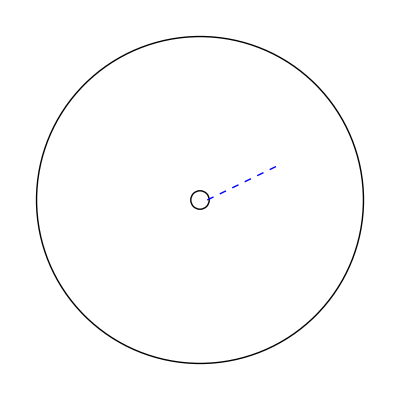

```mathematica
Show[{gomega,gdfn}]
```